```mathematica
T=100; (*максимальний час*)
S=10;(*радіус квадрата (половина сторони)*)
Du=0.05; (*просторова дифузія зайців*)
Dv=0.05;(*просторова дифузія вовків*)
ru=0.2; (*коефіцієнт безумовного росту зайців*)
rv=-0.1;(*коефіцієнт безумовного росту вовків*)
auv=0.2; (*коефіцієнт впливу вовків на кількість зайців*)
avu=-0.2;(*коефіцієнт впливу зайців на кількість вовків*)
auu=0.00; (*коефіцієнт ефекту надлишкової популяції зайців. Якщо сильно відмінне від 0, цикли з часом зникають*)
avv=0.00; (*коефіцієнт ефекту надлишкової популяції вовків. Якщо сильно відмінне від 0, цикли з часом зникають*)
(*Create initial data for u and v*)
gridPoints=5;
SeedRandom[2];
datau=Flatten[Table[{x,y,If[Abs[x]==S||Abs[y]==S,0,RandomReal[{1,2}]]},{x,-S,S,2 S/gridPoints},{y,-S,S,2 S/gridPoints}],1];
datav=Flatten[Table[{x,y,If[Abs[x]==S||Abs[y]==S,0,RandomReal[{1,2}]]},{x,-S,S,2 S/gridPoints},{y,-S,S,2 S/gridPoints}],1];
(*Create interpolating functions for initial conditions*)
initu=Interpolation[datau,Method->"Spline"];
initv=Interpolation[datav,Method->"Spline"];
```

```mathematica
solClassic=NDSolve[{u'[t]== u[t]*(ru-auu*u[t]-auv * v[t]),v'[t]== v[t](rv-auu*u[t]-avu*u[t]),u[0]==initu[0,0],v[0]==initv[0,0]},{u,v},{t,0,T}];
Plot[Evaluate[{u[t],v[t]}/. solClassic],{t,0,T},PlotLabels->{"Жертва","Хижак"},PlotStyle->{Red,Blue},AxesLabel->{"Час","Популяція"},GridLines->Automatic]
```

-Graphics-

```mathematica
sol=NDSolve[{D[u[t,x,y],t]== Du*(D[u[t,x,y],x,x]+D[u[t,x,y],y,y])+u[t,x,y]*(ru-auu*u[t,x,y]-auv*v[t,x,y]),
		       D[v[t,x,y],t]== Dv*(D[v[t,x,y],x,x]+D[v[t,x,y],y,y])+v[t,x,y]*(rv-avv*v[t,x,y]-avu*u[t,x,y]),
			u[0,x,y]==initu[x,y],v[0,x,y]==initv[x,y],
			u[t,-S,y]==0,v[t,-S,y]==0,u[t,S,y]==0,v[t,S,y]==0, (*обмеження на краях області*)
			u[t,x,-S]==0,v[t,x,-S]==0,u[t,x,S]==0,v[t,x,S]==0},
			{u,v},{t,0,T},{x,-S,S},{y,-S,S},
Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->500}}
]
```

{{u→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

```mathematica
Manipulate[Plot3D[Evaluate[{u[t,x,y],v[t,x,y]}/. First[sol]],{x,-10,10},{y,-10,10},PlotRange->All,PlotLegends->{"u (Жертва)","v (Хижак)"},AxesLabel->{"x","y","Популяція"}],{t,0,T}]
```

```mathematica
Manipulate[Plot[Evaluate[{u[t,x,y],v[t,x,y]}/. sol],{t,0,T},PlotLabels->{"Жертва","Хижак"},PlotStyle->{Red,Blue},
AxesLabel->{"Час","Популяція"},GridLines->Automatic],{x,-10,10}, {y,-10,10}]
```

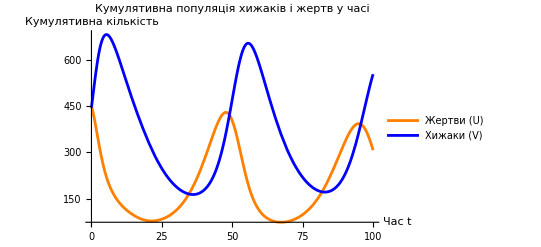

```mathematica
cumulativeU[t_]:=Integrate[Evaluate[u[t,x,y]/. sol],{x,-S,S},{y,-S,S}]
cumulativeV[t_]:=Integrate[Evaluate[v[t,x,y]/. sol],{x,-S,S},{y,-S,S}]
(*Графік*)
Plot[{cumulativeU[t],cumulativeV[t]},{t,0,T},
PlotStyle->{Orange,Blue},
PlotLegends->{"Жертви (U)","Хижаки (V)"},
AxesLabel->{"Час t","Кумулятивна кількість"},
PlotLabel->"Кумулятивна популяція хижаків і жертв у часі"]
```